Fluid flow is a natural phenomenon that is easy to take for granted, a common assumption being that the motion of fluids such as water or air is natural and very basic. However, with deeper analysis the motion of simple fluids such as water is much more complicated and intricate than expected and when modeled with the Navier-Stokes equations leads to some very complex and realistic behavior. In this project, the motion of fluids is modeled using the Navier-Stokes equations for laminar fluid flow, and then uses the results to analyze the optimal orientations of different shapes in this flow. This is applicable to real-world scenarios such as wind tunnels and fluidic machine modeling. In addition, the same logic can be used to model other examples in fluid dynamics such as fluidic oscillators and fluid flow through technical objects.

## Introduction

The Navier-Stokes Equations are a set of equations that model ideal fluid flow, from simulating wind tunnels to the flow of rivers. In this project, the Navier-Stokes Equations were used to simulate 2D and 3D laminar flow in static shapes. This project explores the applications of this approach from modelling the optimal orientation and rotational paths of objects in channel flow, to using the same fluid logic to create other famous examples in the field of fluid dynamics, including a simulation of a fluidic oscillator. Simulating fluids in this way involves the use of Partial Differential Equations (PDEs), specifically generating them from the applicable Navier-Stokes equations to a geometric configuration and solving them with specified boundary conditions with the Wolfram Language in order to generate vector fields that represent the flow of the fluid in the specified geometric configuration. This vector-field based approach can be used to model complex fluid behavior (permitted that the simulation resolution used is acceptable) including the applications that are presented below.

## The Navier-Stokes Equations

The Navier-Stokes Equations are a set of partial differential equations (PDEs) that describe the motion of viscous fluid substances. The two Navier-Stokes equations that apply to the fluid flows simulated in this project are the Continuity Equation and the Momentum Equation, modeling the conservation of mass and the conservation of momentum respectively.

### Variables and their Meanings

```mathematica
[{
<|"Variable"-> "u", "Definition"->"velocity vector field"|>,
<|"Variable"-> "p", "Definition"->"pressure"|>,
<|"Variable"-> "∇p", "Definition"->"pressure gradient"|>,
<|"Variable"-> "μ∇^2 ", "Definition"->"viscous forces"|>,
<|"Variable"-> "f", "Definition"->"external forces"|>,
<|"Variable"-> "μ", "Definition"->"dynamic viscosity (constant)"|>,
<|"Variable"-> "ρ", "Definition"->"fluid density (constant)"|>},PlotTheme->"Detailed",Alignment->{Left,Center}]
```

Variable | Definition
u | velocity vector field
p | pressure
∇p | pressure gradient
μ∇^2  | viscous forces
f | external forces
μ | dynamic viscosity (constant)
ρ | fluid density (constant)

### The Continuity Equation (Conservation of Mass)

(∂ρ)/(∂t)+∇•(ρu)=0

For incompressible fluids, the pressure gradient is constant, and as a result the equation simplifies to the following

∇•u=0

### The Momentum Equation (Conservation of Momentum)

ρ((∂u)/(∂t) + u + ∇u) = -∇p + μ∇^2 + f

The momentum equation describes the conservation of momentum in fluids, ensuring that each particle of fluid shares its momentum with other fluid particles in accordance with the laws of physics.
Note that the f in the equation represents any external forces acting on the fluid, (e.g. gravity). In this simulation, gravity is assumed to be negligible, so the f term is not used.

## Applying Navier-Stokes Equations

Converting the Navier-Stokes equations into code involves using the Wolfram Language Functions that solve PDEs. In this project, NDSolve is used to solve PDEs numerically as opposed to solving them symbolically which can be done with DSolve in Wolfram Language.

### Simplifying the Navier-Stokes Equations

A common technique when analyzing fluids using the Navier-Stokes equations is to combine the Continuity and Momentum equations into one, this can be done using the following simplification.
Writing the momentum equation with the viscous stress tensor τ which describes internal stress on the fluid:

-Graphics-

Knowing that the viscous stress tensor τ is given as:

Further integrating the definition that ϵ is :

-Graphics-

Finally combining the two equations, the resulting equation is:

-Graphics-

### Solving the Navier-Stokes Equations Simultaneously

Before moving on, a simple check can be done to verify the integrity of the derivation so far.

-Graphics-

The units work out, following Newton’s second law of motion F = ma. With the current, simplified state of the momentum equation, it can be easily substituted into the mass conservation equation: 



Finally combining the two equations, the resulting equation is: 
 
-Graphics-

### Converting Equations into Component Form

Converting the resulting equation into component form, we obtain the following:

-Graphics-

For a constant dynamics viscosity μ a further simplification is possible, resulting in:

-Graphics-

## Implementing Static Fluids

Import the NDSolve package for future mesh generation and other useful utilities.

```mathematica
Needs["NDSolve`FEM`"]
$HistoryLength = 0;
```

In order to simulate static fluids inside a container, this project uses Wolfram Language Regions for easy integration into various plotting and mathematical functions. The region for the static fluid is defined below.

Create a semi-complex rectangular region using RegionUnion and Visualize:

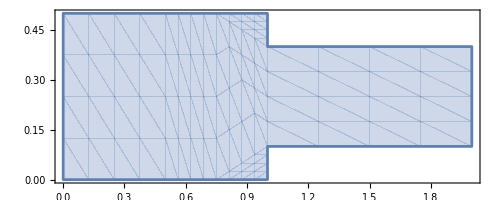

```mathematica
Ω=RegionUnion[Rectangle[{0,0},{1,1/2}],Rectangle[{1,1/10},{2,2/5}]];
RegionPlot[Ω,AspectRatio->Automatic]
```

Set up the fluid parameters and the static fluid variables that will eventually model the x and y velocity along with the pressure:

```mathematica
vars={{u[x,y],v[x,y],p[x,y]},{x,y}};
pars=<|"DynamicViscosity"->Quantity[0.934,"Pascals"  "Seconds"],
"MassDensity"->Quantity[1.25,("Grams")/("Centimeters")^3]|>;
```

The initial velocity in the x-direction is prescribed through the boundary conditions. This is done by specifying an inflow profile for the u dependent variable on the left-hand side of the region. On the bottom and upper part of the region, a wall boundary condition is specified. Wall boundary conditions are specified by setting the u and v components to 0, this will ensure that the model displacement in those places is 0. An outflow condition is set on the right-side of the domain, and in this case we set the pressure to 0 for simplicity. In general each dependent variable (u, v) should either have a Dirichlet condition or a Robin-type Neumann specified. A pure Neumann value like Neumann 0 is not sufficient- this will lead to the solution to only be accurate to a constant. Dirichlet Boundary Conditions can be used to model velocity and pressure specification as well as modelling physical constraints. Neumann Boundary Conditions can be used to model Shear Stress or the rate of change of a variable across a boundary (like pressure or displacement),  they can also be used to model Natural Boundaries where the physical problem will naturally dictate the flux of momentum or mass. For example, in free-surface flows, specifying the normal stress on the free-surface boundary helps maintain consistency with fluid dynamics principles.

The next step is to set up the Fluid Flow PDE, luckily for static fluids, Wolfram Language provides functions specifically for this task.

Set up the Fluid Flow PDE Component (op stands for operating parameters, pars stands for fluid parameters)

```mathematica
MatrixForm[op=FluidFlowPDEComponent[vars,pars]];
```

As specified above, the next step is to set up the simple boundary conditions in terms of plot space

```mathematica
bcs={
DirichletCondition[{u[x,y]==4*0.3*y*(0.5-y)/(0.41)^2,v[x,y]==0.},x==0.],
DirichletCondition[{u[x,y]==0.,v[x,y]==0.},0<x<2],
DirichletCondition[p[x,y]==0.,x==2]};
```

A stable solution for the boundary conditions can be found if the velocities are interpolated with a higher order than the pressure. This helps create more accuracy of values between grid points with the help of higher degree polynomial or interpolation schemes. The pressure variable is normally of a lower order meaning that pressure is often approximated using simpler interpolation schemes or at a coarser level (larger grid spaces) compared to velocities. This approach is often chosen because pressure variations tend to be smoother and less sensitive to numerical errors when compared to velocities.

Finally, we can solve the PDE

```mathematica
{uVel,vVel,pressure}=NDSolveValue[{op=={0,0,0},bcs},{u,v,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1}}];
```

Plotting the resulting geometry to verify the realism of the solution

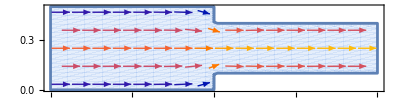

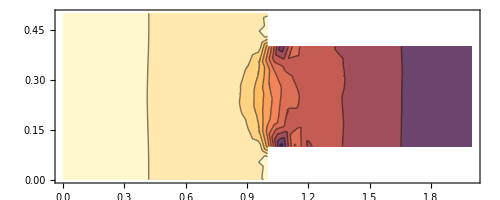

```mathematica
VectorPlot[{uVel[x,y],vVel[x,y]},{x,y}∈Ω,AspectRatio->Automatic]
ContourPlot[pressure[x,y],{x,y}∈Ω,AspectRatio->Automatic]
```

This is the framework for all future “simulations.”
	1. Set up environment
	2. Create the Fluid flow matrix 
	3. Set up boundaries with conditions
	4. Solve the resulting PDE for u, v, and p
	5. Visualize results through velocity vectors and pressure graphs

### Application: Fluid in a Rectangle-Non-Slip Condition (Top Wall Treadmill)

This example is a common example in fluid dynamics and verifies that the realism of the fluid simulation framework while exploring non-slip boundaries. Here, a rectangular region is filled with a fluid and a mechanism is created to drive the fluid in the positive x-direction like a conveyor belt. It is important to note that there are two types of boundaries, slip and non-slip. Normally, a fluid will flow and collide with a wall and effectively ‘slip’ against it, basically the wall has no effect on the resulting velocity of the fluid. In the no-slip case, the wall can have a velocity and at points along those walls, the fluid velocity will be set to 0, essentially moving the fluid with the wall through a low pressure zone between the fluid and the wall.

Set up the fluid variables and a slightly different simulation environment, like before

```mathematica
vars={{u[x,y],v[x,y],p[x,y]},{x,y}};
Ω=Rectangle[{0,0},{1,1}];
```

Set up the fluid flow PDE (also like before)

```mathematica
pars=<|"ReynoldsNumber"->1000|>;
pde=FluidFlowPDEComponent[vars,pars]=={0,0,0};
```

Set up the boundary conditions and solve the Fluid Flow PDE

```mathematica
top=DirichletCondition[{u[x,y]==1,v[x,y]==0},y==1];
wall=DirichletCondition[{u[x,y]==0,v[x,y]==0},y<1];
referencePressure=DirichletCondition[p[x,y]==0,x==0&&y==0];

bcs={top,wall,referencePressure};
{uVel,vVel,pressure}=NDSolveValue[{pde,bcs},vars[[1]],{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1}}];
```

Visualizing the pressure as a scalar field. Both Contour and Density plots work well for this

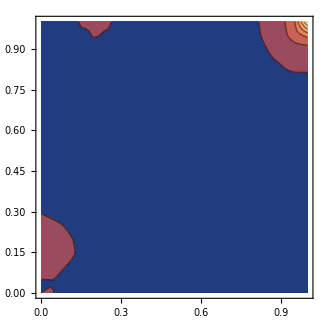

```mathematica
ContourPlot[pressure,{x,y}∈Ω,PlotRange->All]
```

Visualize the velocities using vector and stream plots, creating a framework for future use

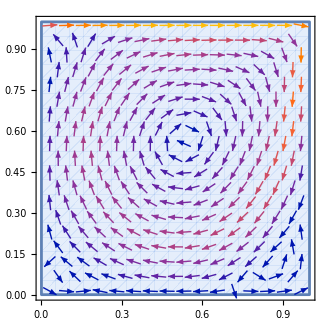

```mathematica
VectorPlot[{uVel,vVel},{x,y}∈Ω]
```

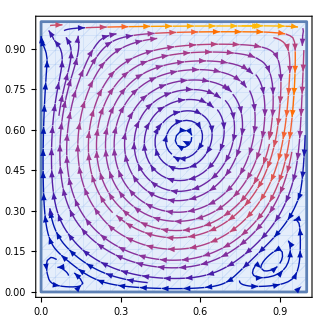

```mathematica
StreamPlot[{uVel,vVel},{x,y}∈Ω]
```

#### Parametric Analysis- Comparing the Flow Field for Various Reynolds Numbers

This section will make use of the ParametricNDSolve function which works just like NDSolve, with the addition that parameters can be specified. ParamatricNDSolve will then return a function, then when fed numerical values for the parameters will compute the numerical solution.

Starting by setting a symbolic Reynolds Number (Re)

```mathematica
pars = <|"ReynoldsNumber" -> re|>;
```

Set up the Fluid Flow PDE

```mathematica
pde=FluidFlowPDEComponent[vars,pars]=={0,0,0};
```

Set up a parametric function for different Reynolds Numbers

```mathematica
pfun=ParametricNDSolveValue[{pde,bcs},vars[[1]],{x,y}∈Ω,re,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1}}];
```

Compute the solutions for different Re’s

```mathematica
solutions=pfun/@Range[1, 5000, 100];
```

Find the positions of the largest gradients of the u and v velocity for the last computed Reynolds number

```mathematica
GraphicsRow[ContourPlot[Evaluate[Sqrt[Total[Grad[#,{x,y}]^2]]],{x,y}∈Ω,PlotRange->All]&/@solutions[[-1,{1,2}]]]
```

-Graphics-

To visualize the pressure differences better, it is necessary to reflect the steeper gradients by having a finer resolution at steeper gradients. Seeing that the flow gradient is higher at the walls, a graded mesh will be best for this task. This allows for refinements while not increasing the overall number of elements by too much.

The following code generates a graded mesh (m1) and then multiplies it with itself to increase the resolution at the corners

```mathematica
m1=ToGradedMesh[Line[{{0},{1}}],<|"Alignment"->"BothEnds","ElementCount"->75|>];
mesh=ElementMeshRegionProduct[m1,m1]
```

ElementMesh[{{0.,1.},{0.,1.}},{QuadElement[<5625>]}]

Visualizing the mesh:

```mathematica
mesh["Wireframe"];
```

Create a new parametric function, but this time using the constructed mesh:

```mathematica
pfun=ParametricNDSolveValue[{pde,bcs},vars[[1]],{x,y}∈mesh,re,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1}}]
```

ParametricFunction[<>]

Compute more solutions for the purpose of creating an animation:

```mathematica
reynoldsNumbers={100,400,1000,3200,5000,7500,10000};
solutions=pfun/@reynoldsNumbers;
```

Extract a few mesh points to be used as StreamPoints (determines how many stream lines to draw)

```mathematica
pts=Take[Flatten[m1["Coordinates"]],{1,-1,10}]
```

{0.,0.0781546,0.188239,0.343296,0.556831,0.740856,0.871506,0.964261,0.0319161,0.12311,0.25156,0.432486,0.647389,0.805148,0.91715,0.996667}

```mathematica
frames=MapThread[(StreamPlot[#1,{x,y}∈mesh,StreamPoints->{Tuples[pts,2],Automatic,1},StreamMarkers->None,RegionFillingStyle->None,PlotLabel->"Reynolds Number: "<>ToString[#2],Frame->None]/. Arrow->Line)&,{solutions[[All,{1,2}]],reynoldsNumbers}];frames=Rasterize[#,"Image",ImageResolution->120]&/@frames;
anim = ListAnimate[frames];
```

```mathematica
EmbeddedService[{"Vimeo","982135617"}]
```

Null<iframe\r
  src="https://player.vimeo.com/video/982135617?title=0&byline=0&portrait=0"…der="0"\r
  webkitallowfullscreen\r
  mozallowfullscreen\r
  allowfullscreen></iframe>\r
<iframe

  src="https://player.vimeo.com/video/982135617?title=0&byline=0&portrait=0"

  width="500"

  height="281"

  frameborder="0"

  webkitallowfullscreen

  mozallowfullscreen

  allowfullscreen></iframe>

#### Comparing Results With Known Benchmarks

Before moving on to non-static fluid flow, it is important to get a quantitative measure for how well the current simulation compares to more “official” sources.

Import the Benchmark Results (vx and uy data represent benchmark data for x and y velocity respectively)

```mathematica
uyData=Import[FileNameJoin[{$InstallationDirectory,"SystemFiles","Components","PDEModels","SupportFiles","LidDrivenCavityBenchmarkUY.wdx"}]];
vxData=Import[FileNameJoin[{$InstallationDirectory,"SystemFiles","Components","PDEModels","SupportFiles","LidDrivenCavityBenchmarkVX.wdx"}]];
```

Compare the computed solution at x=1/2 with the benchmark results for different Reynolds Numbers

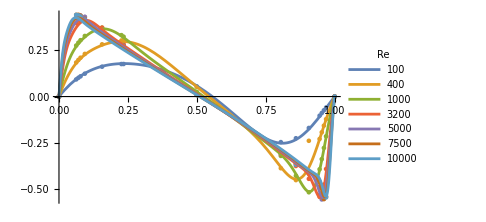

```mathematica
Show[ListPlot[vxData],Plot[Evaluate[Through[solutions[[All,2,0]][x,0.5]]],{x,0,1},PlotLegends->LineLegend[reynoldsNumbers,LegendLabel->"Re"]],ImageSize->Medium]
```

The results, while not completely exact, seem pretty close to accurate laminar flow, especially for higher Re’s.

The same process is applied for y=1/2

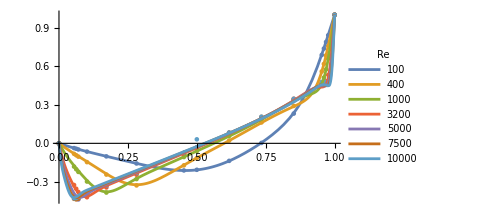

```mathematica
Show[ListPlot[uyData],Plot[Evaluate[Through[solutions[[All,1,0]][0.5,y]]],{y,0,1},PlotLegends->LineLegend[reynoldsNumbers,LegendLabel->"Re"]],ImageSize->Medium]
```

## Simulating Fluid Flow Around Static Obstacles

In this section, we use the same equations as for static fluids but extend the approach to work around obstacles, expanding the boundary conditions that were set in the previous section and allowing for more complex behavior.

Start by setting up the dimensions for the new boundary region, which will be a large square with evenly spaced smaller square cutouts as the obstacles
L is the length of the square region and x1 and y1 define the base coordinates of the β sub-rectangles

```mathematica
L=3;
x1=L/4;​​
y1=L/4;​​
```

Define the fluid flow region based on the parameters above. This will create the large enclosure as well as the square cutouts

```mathematica
α=Rectangle[{0,0},{L,L}];​​
β1=Rectangle[{x1/2,y1/2},{7*x1/4,7*y1/4}];​​
β2=Rectangle[{x1/2,y1/4+L/2},{7*x1/4,6*y1/4+L/2}];​​
β3=Rectangle[{x1/4+L/2,y1/2},{3*x1/2+L/2,7*y1/4}];​​
β4=Rectangle[{x1/4+L/2,y1/4+L/2},{3*x1/2+L/2,3*y1/2+L/2}];
```

Combine the regions using RegionUnion and then take the difference from the enclosure to create a simple obstacle course for the fluid flow

```mathematica
Clear[K];
Clear[Ω];

K=RegionUnion[β1,β2,β3,β4];
​​Ω=RegionDifference[Rectangle[{0,0},{L,L}], K];
```

Set up variable functions to compute x-velocity, y-velocity, and pressure (similar to the static fluids section)

```mathematica
Clear[xVel];
Clear[yVel];
Clear[pressure];

xVel[0][x_,y_]:=0;
yVel[0][x_,y_]:=0;
pressure[0][x_,y_]:=0;
```

Define the mesh and display it in a wireframe

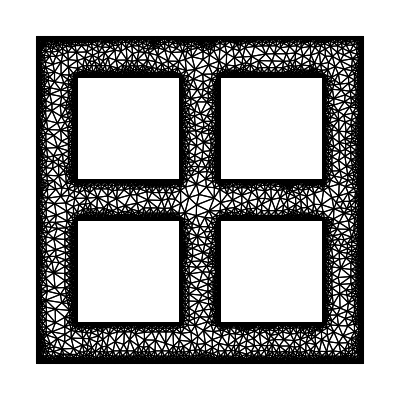

```mathematica
mesh=ToElementMesh[​​Ω,"MaxBoundaryCellMeasure"->0.005,"MeshElementType"->TriangleElement];
mesh["Wireframe"]
```

Define a discrete time step as well as the Navier-Stokes Equations to solve

```mathematica
dt=0.02;op1[i_]={ρ((u[x,y]-xVel[i-1][x,y])/dt+xVel[i-1][x,y]D[u[x,y], x]+yVel[i-1][x,y]  D[u[x,y], y])-μ (D[u[x,y], x,x]+D[u[x,y], y,y])+D[p[x,y], x]==0,ρ((v[x,y]-yVel[i-1][x,y])/dt+xVel[i-1][x,y]D[v[x,y], x]+yVel[i-1][x,y]  D[v[x,y], y])-μ (D[v[x,y], x,x]+D[v[x,y], y,y])+D[p[x,y], y]==0,D[u[x,y], x]+D[v[x,y], y]==0}/.{ρ->1,μ->10^-4};
```

Define the boundary conditions for this region (inflow, outflow, and walls)

```mathematica
boundaryconditions1={DirichletCondition[{u[x,y]==0.,v[x,y]==0.},True],DirichletCondition[p[x,y]==0,x==1],DirichletCondition[p[x,y]==1,x==0]};
```

Solve the PDE’s using Table (not as optimal as before)

```mathematica
Table[{xVel[i],yVel[i],pressure[i]}=NDSolveValue[{op1[i],boundaryconditions1},{u,v,p},{x,y}∈mesh,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1}}],{i,1,15}];
```

Plot the results using StreamPlot

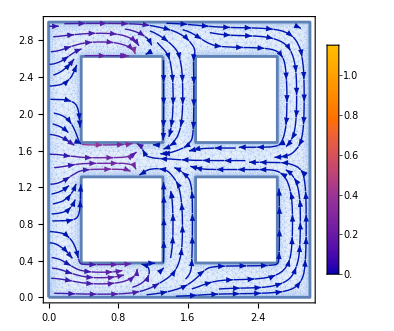

```mathematica
currenttime = 7;
StreamPlot[{xVel[currenttime][x,y],yVel[currenttime][x,y]},{x,y}∈xVel[currenttime]["ElementMesh"],AspectRatio->Automatic,PlotRange->All,PlotLegends->Automatic,ImageSize->Medium]
```

This approach works well with fluid flow coming in from the left and exiting from the right, but this approach can also be extended to fluid flows from other directions, including diagonal fluid flow. In the following example, the boundary conditions will be adjusted so that the flow will originate from the top left corner.

Set up the new boundary conditions for diagonal flow

```mathematica
boundaryconditionsdiagonalflow={DirichletCondition[{u[x,y]==0.,v[x,y]==0.},True],DirichletCondition[p[x,y]==0,x==L&&y<L],DirichletCondition[p[x,y]==1,x==0],DirichletCondition[p[x,y]==0,y==0&&x>0],DirichletCondition[p[x,y]==1,y==L]};
```

Solve the new set of PDE’s using Table

```mathematica
Table[{xVel[i],yVel[i],pressure[i]}=NDSolveValue[{op1[i],boundaryconditionsdiagonalflow},{u,v,p},{x,y}∈mesh,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1}}],{i,1,15}];
```

Plot the results

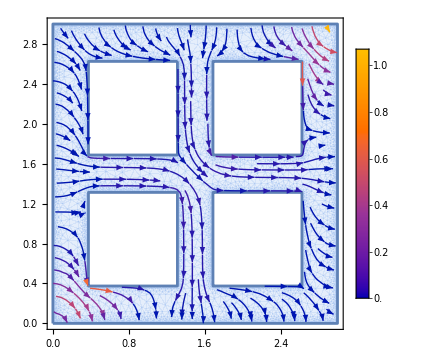

```mathematica
currenttime = 9;
StreamPlot[{xVel[currenttime][x,y],yVel[currenttime][x,y]},{x,y}∈xVel[currenttime]["ElementMesh"],AspectRatio->Automatic,PlotRange->All,PlotLegends->Automatic,ImageSize->Medium]
```

## Simulating Object Balance Points in Dynamic 2-D Laminar Flow

With an accurate framework for simulating static fluids, we can extend the same Navier-Stokes Equations to represent inflow and outflow conditions, effectively modelling a flowing fluid.

Starting by defining a square region and some coordinates for objects to be rendered
L and H have to be cleared so that the variable names are free to be re-assigned to the new fluid simulation region

```mathematica
Clear[L];
Clear[H];

H= 0.93808315196;L=0.93808315196;
{x0,y0,r0}={.5,.5,1/20};
```

#### Defining Shape Regions, From Simple Polygons to Complex Shapes

This is the part of the project where the capability of Wolfram Language’s Region functions is used extensively, as they are fairly easy to work with and can model some complex behavior with a few simple manipulations.

Defining an “A”-style letter contour

```mathematica
scalingFactor=0.2;
outerTriangle=Polygon[{{x0,y0}+scalingFactor*({-0.4,-0.3}),
{x0,y0}+scalingFactor*({0.4,-0.3}),{x0,y0}+scalingFactor*({0,0.45})}];
innerTriangle=Polygon[{{x0,y0}+scalingFactor*({-0.3,-0.3}),{x0,y0}+scalingFactor*({0.3,-0.3}),{x0,y0}+scalingFactor*({0,0.35})}];
letterARegion=Region[RegionDifference[outerTriangle,innerTriangle]];
```

Defining a letter “B”- style contour

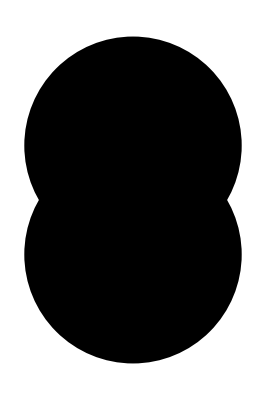

```mathematica
circ1 = Disk[{x0, y0}, r0];
circ2 = Disk[{x0, y0+  r0}, r0];

BReg = Region[RegionUnion[circ1, circ2]]
```

Defining a Variable Star-Style Region

```mathematica
starRegion=RegionUnion@@Table[RegularPolygon[{x0, y0},{r0,t Pi/6},3],{t,6}];
```

Specify which region to use for the simulation

```mathematica
fluidFlowRegion =starRegion;
```

#### Method for Analyzing Dynamic Laminar Flow

In this project, the method for analyzing rotation of different shapes, two copies of the region are created, one to simulate flow in a channel without any obstacles, and the other to simulate channel flow but in a region with the shape cut out. This has the same effect as simulating fluid motion around that region specifically (assuming that region stays still). The original copy comes into use when visualizing, so that the only part of the animation that is in motion is the shape that is being rotated.

Clear the previous definitions of the regions to avoid ambiguity

```mathematica
Clear[Ω];
Clear[Ω1];
```

Define the Fluid Flow Regions, where the simulations will take place

```mathematica
Ω=RegionDifference[Rectangle[{0,0},{L,H}], fluidFlowRegion];
Ω1=Region[Rectangle[{0,0},{L,H}]];

Rasterize[RegionPlot[Ω,AspectRatio->Automatic]]
Rasterize[RegionPlot[Ω1, AspectRatio-> Automatic]]

Ω = ToElementMesh[Ω, MaxCellMeasure -> 0.001];
Ω1 = ToElementMesh[Ω1, MaxCellMeasure -> 0.001];
```

-Graphics-

-Graphics-

Extract vertices from the polygon to be used as potential pivot points later in the simulation (this can generate more complex behavior than just a pivot around a centroid)

```mathematica
polygons=RegionBoundary[fluidFlowRegion]/. Line[pts_]:>pts;

vertices=Flatten[polygons,1];

uniqueVertices=DeleteDuplicates[vertices];

vertexPoints = Table[{uniqueVertices[[i]], uniqueVertices[[i + 1]]}, {i, 1, Length[uniqueVertices]- 1}];
```

In the case of flowing fluids, we solve the PDE’s using Time Integration which is easy enough to implement and finds a solution to dynamic boundaries as specified in the boundary conditions.

Set up Time Integration Variables and Interpolation Functions which are used for future visualization
Clear previous definitions of the Time Integration Variables and Interpolation Functions

```mathematica
Clear[K];

Clear[UX];
Clear[VY];
Clear[P0];

Clear[UX1];
Clear[VY1];
Clear[P01];

Clear[U0];
Clear[U01];

K=400;Um=1.5;ν=10^-3;t0=.02;
U0[y_,t_]:=4*Um*y/H*(1-y/H)*Sin[Pi*t/8]
U01[y_,t_]:=4*Um*y/H*(1-y/H)*Sin[Pi*t/8]

UX[0][x_,y_]:=0;
VY[0][x_,y_]:=0;
P0[0][x_,y_]:=0;

UX1[0][x_,y_]:=0;
VY1[0][x_,y_]:=0;
P01[0][x_,y_]:=0;
```

Solve the PDE’s for both regions (channel and channel with obstacle)

```mathematica
Do[
{UX[i],VY[i],P0[i]}=NDSolveValue[{{({{-μ,0},{0,-μ}}.u[x,y]{x,y}Inactive){x,y}Inactive+Derivative[1,0][p][x,y]+(u[x,y]-UX[i-1][x,y])/t0+UX[i-1][x,y]*D[u[x,y],x]+VY[i-1][x,y]*D[u[x,y],y],({{-μ,0},{0,-μ}}.v[x,y]{x,y}Inactive){x,y}Inactive+Derivative[0,1][p][x,y]+(v[x,y]-VY[i-1][x,y])/t0+UX[i-1][x,y]*D[v[x,y],x]+VY[i-1][x,y]*D[v[x,y],y],Derivative[1,0][u][x,y]+Derivative[0,1][v][x,y]}=={0,0,0}/.μ->ν,{
DirichletCondition[{u[x,y]==U0[y,i*t0],v[x,y]==0},x==0.],DirichletCondition[{u[x,y]==0.,v[x,y]==0.},0≤x≤L&&y==0||y==H],DirichletCondition[{u[x,y]==0,v[x,y]==0},(x-x0)^2+(y-y0)^2==r0^2],DirichletCondition[p[x,y]==P0[i-1][x,y],x==L]}},{u,v,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1},"MeshOptions"->{"MaxCellMeasure"->0.001}}],{i,1,K}];
```

```mathematica
Do[
{UX1[i],VY1[i],P01[i]}=NDSolveValue[{{({{-μ,0},{0,-μ}}.u[x,y]{x,y}Inactive){x,y}Inactive+Derivative[1,0][p][x,y]+(u[x,y]-UX1[i-1][x,y])/t0+UX1[i-1][x,y]*D[u[x,y],x]+VY1[i-1][x,y]*D[u[x,y],y],({{-μ,0},{0,-μ}}.v[x,y]{x,y}Inactive){x,y}Inactive+Derivative[0,1][p][x,y]+(v[x,y]-VY1[i-1][x,y])/t0+UX1[i-1][x,y]*D[v[x,y],x]+VY1[i-1][x,y]*D[v[x,y],y],Derivative[1,0][u][x,y]+Derivative[0,1][v][x,y]}=={0,0,0}/.μ->ν,{
DirichletCondition[{u[x,y]==U01[y,i*t0],v[x,y]==0},x==0.],DirichletCondition[{u[x,y]==0.,v[x,y]==0.},0≤x≤L&&y==0||y==H],DirichletCondition[{u[x,y]==0,v[x,y]==0},(x-x0)^2+(y-y0)^2==r0^2],DirichletCondition[p[x,y]==P01[i-1][x,y],x==L]}},{u,v,p},{x,y}∈Ω1,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1},"MeshOptions"->{"MaxCellMeasure"->0.001}}],{i,1,K}];
```

Plot the Pressure Distribution in Both Channels

```mathematica
{ContourPlot[UX1[K/2][x,y],{x,y}∈Ω1, AspectRatio->Automatic,ColorFunction->"BlueGreenYellow",FrameLabel->{x,y},PlotLegends->Automatic,Contours->20,PlotPoints->25,PlotLabel->u,MaxRecursion->2],ContourPlot[UX[K/2][x,y],{x,y}∈Ω, AspectRatio->Automatic,ColorFunction->"BlueGreenYellow",FrameLabel->{x,y},PlotLegends->Automatic,Contours->20,PlotPoints->25,PlotLabel->v,MaxRecursion->2,PlotRange->All]}//Quiet
```

We can also plot the same relation using a Density Plot

```mathematica
{DensityPlot[UX1[K][x,y],{x,y}∈Ω1, AspectRatio->Automatic,ColorFunction->"BlueGreenYellow",FrameLabel->{x,y},PlotLegends->Automatic,PlotPoints->25,PlotLabel->u,MaxRecursion->2],DensityPlot[UX[K][x,y],{x,y}∈Ω, AspectRatio->Automatic,ColorFunction->"BlueGreenYellow",FrameLabel->{x,y},PlotLegends->Automatic,PlotPoints->25,PlotLabel->v,MaxRecursion->2,PlotRange->All]}//Quiet
```

Finally, we can animate the fluid flow using a DensityPlot

```mathematica
Animate[Quiet@Module[{sol},{UX1[i],VY1[i],P01[i]}=Quiet@NDSolveValue[{Inactive[Div][{{-μ,0},{0,-μ}}.Inactive[Grad][u[x,y],{x,y}],{x,y}]+Derivative[1,0][p][x,y]+(u[x,y]-UX1[i-1][x,y])/t0+UX1[i-1][x,y]*Derivative[1,0][u][x,y]+VY1[i-1][x,y]*Derivative[0,1][u][x,y]==0,Inactive[Div][{{-μ,0},{0,-μ}}.Inactive[Grad][v[x,y],{x,y}],{x,y}]+Derivative[0,1][p][x,y]+(v[x,y]-VY1[i-1][x,y])/t0+UX1[i-1][x,y]*Derivative[1,0][v][x,y]+VY1[i-1][x,y]*Derivative[0,1][v][x,y]==0,Derivative[1,0][u][x,y]+Derivative[0,1][v][x,y]==0/. μ->ν,DirichletCondition[{u[x,y]==U01[y,i*t0],v[x,y]==0},x==0.],DirichletCondition[{u[x,y]==0.,v[x,y]==0.},0<=x<=L&&y==0||y==H],DirichletCondition[{u[x,y]==0,v[x,y]==0},(x-x0)^2+(y-y0)^2==r0^2],DirichletCondition[p[x,y]==P01[i-1][x,y],x==L]},{u,v,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1},"MeshOptions"->{"MaxCellMeasure"->0.001}}];
DensityPlot[UX1[i][x,y],{x,y}∈Ω1,AspectRatio->Automatic,ColorFunction->"BlueGreenYellow",FrameLabel->{x,y},PlotLegends->Automatic,PlotPoints->25,PlotLabel->StringForm["u at Time t=1",i*t0],MaxRecursion->2]],{i,1,K,1},AnimationRunning->False, AnimationRepetitions->1] // Quiet;
```

Animation as GIF Below

```mathematica
AnimatedImage[Import[NotebookDirectory[]<>"FlowWoObj.gif"], ImageSize->Medium]
```

Next, we can animate the rotation of the selected object without the fluid

```mathematica
Animate[Module[{angularVelocity,x0=0.1,y0=H/2,u,v,angle,rotatedVertices=vs,rotationMatrix},(*Evaluate interpolating functions*){u,v}={UX[i][x,y],VY[i][x,y]};
(*Calculate angular velocity*)angularVelocity=0.5  (D[v,x]-D[u,y])/. {x->x0,y->y0};
(*Integrate angular velocity to get angle*)angle=NIntegrate[angularVelocity,{t,0,i*t0}];
centroid=RegionCentroid[fluidFlowRegion];
pivotPoint = centroid;

fluidFlowRegion=TransformedRegion[fluidFlowRegion,RotationTransform[angle,pivotPoint]];
pivot = Disk[pivotPoint, 0.005];
plotRegion = fluidFlowRegion;
RegionPlot[plotRegion,PlotRange->{{0,L},{0,H}},AspectRatio->Automatic]],{i,1,K},AnimationRunning->False, AnimationRepetitions->1] // Quiet;
```

Animation as GIF Below

```mathematica
EmbeddedService[{"Vimeo", "982135575" }]
```

Null<iframe\r
  src="https://player.vimeo.com/video/982135575?title=0&byline=0&portrait=0"…der="0"\r
  webkitallowfullscreen\r
  mozallowfullscreen\r
  allowfullscreen></iframe>\r
<iframe

  src="https://player.vimeo.com/video/982135575?title=0&byline=0&portrait=0"

  width="500"

  height="281"

  frameborder="0"

  webkitallowfullscreen

  mozallowfullscreen

  allowfullscreen></iframe>

Animate the star moving around a fixed pivot point (not the center)

```mathematica
Animate[Module[{angularVelocity,x0=0.1,y0=H/2,u,v,angle,rotatedVertices=vs,rotationMatrix},(*Evaluate interpolating functions*){u,v}={UX[i][x,y],VY[i][x,y]};
(*Calculate angular velocity*)angularVelocity=0.5  (D[v,x]-D[u,y])/. {x->x0,y->y0};
(*Integrate angular velocity to get angle*)angle=NIntegrate[angularVelocity,{t,0,i*t0}];
centroid=RegionCentroid[fluidFlowRegion];
pivotPoint = vertexPoints[[2]];

fluidFlowRegion=TransformedRegion[fluidFlowRegion,RotationTransform[angle,pivotPoint]];
pivot = Disk[pivotPoint, 0.005];
plotRegion = fluidFlowRegion;
RegionPlot[plotRegion,PlotRange->{{0,L},{0,H}},AspectRatio->Automatic]],{i,1,K,1},AnimationRunning->False, AnimationRepetitions->1] // Quiet;
```

Animation as GIF Below

```mathematica
EmbeddedService[{"Vimeo", "982135587" }]
```

Null<iframe\r
  src="https://player.vimeo.com/video/982135587?title=0&byline=0&portrait=0"…der="0"\r
  webkitallowfullscreen\r
  mozallowfullscreen\r
  allowfullscreen></iframe>\r
<iframe

  src="https://player.vimeo.com/video/982135587?title=0&byline=0&portrait=0"

  width="500"

  height="281"

  frameborder="0"

  webkitallowfullscreen

  mozallowfullscreen

  allowfullscreen></iframe>

Now adding the rotation of the object to the fluid flow, we can overlay them on top of each other

```mathematica
Animate[Quiet@Module[{angularVelocity,x0=0.1,y0=H/2,u,v,angle},(*Solve Navier-Stokes equations*){UX[i],VY[i],P0[i]} =Quiet@NDSolveValue[{(*Momentum equations*)Quiet@Inactive[Div][{{-μ,0},{0,-μ}}.Inactive[Grad][u[x,y],{x,y}],{x,y}]+Derivative[1,0][p][x,y]+(u[x,y]-UX[i-1][x,y])/t0+UX[i-1][x,y]*Derivative[1,0][u][x,y]+VY[i-1][x,y]*Derivative[0,1][u][x,y]==0,Quiet@Inactive[Div][{{-μ,0},{0,-μ}}.Inactive[Grad][v[x,y],{x,y}],{x,y}]+Derivative[0,1][p][x,y]+(v[x,y]-VY[i-1][x,y])/t0+UX[i-1][x,y]*Derivative[1,0][v][x,y]+VY[i-1][x,y]*Derivative[0,1][v][x,y]==0,Derivative[1,0][u][x,y]+Derivative[0,1][v][x,y]==0/. μ->ν,(*Boundary conditions*)DirichletCondition[{u[x,y]==U01[y,i*t0],v[x,y]==0},x==0.],DirichletCondition[{u[x,y]==0.,v[x,y]==0.},0<=x<=L&&y==0||y==H],DirichletCondition[{u[x,y]==0,v[x,y]==0},(x-x0)^2+(y-y0)^2==r0^2],DirichletCondition[p[x,y]==P0[i-1][x,y],x==L]},{u,v,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1},"MeshOptions"->{"MaxCellMeasure"->0.001}}];
(*Evaluate interpolating functions*){u,v}={UX[i][x,y],VY[i][x,y]};
angularVelocity=0.5 (D[v,x]-D[u,y])/. {x->x0,y->y0};
angle=NIntegrate[angularVelocity,{t,0,i*t0}];

centroid=RegionCentroid[fluidFlowRegion];
pivotPoint = centroid;
fluidFlowRegion=TransformedRegion[fluidFlowRegion,RotationTransform[angle,pivotPoint]];
Ω2=RegionDifference[Rectangle[{0,0},{L,H}], fluidFlowRegion];

(*Draw graphics*)Show[DensityPlot[UX1[i][x,y],{x,y}∈Ω2,AspectRatio->Automatic,ColorFunction->"BlueGreenYellow",FrameLabel->{x,y},PlotLegends->Automatic,PlotPoints->25,PlotLabel->StringForm["u at Time t=1",i*t0],MaxRecursion->2],ImageSize->500]],{i,1,K,1},AnimationRunning->False, AnimationRepetitions->1] // Quiet;
```

Animation as GIF Below

```mathematica
EmbeddedService[{"Vimeo", "982135547"}]
```

Null<iframe\r
  src="https://player.vimeo.com/video/982135547?title=0&byline=0&portrait=0"\r…rder="0"\r
  webkitallowfullscreen\r
  mozallowfullscreen\r
  allowfullscreen></iframe>\r
<iframe

  src="https://player.vimeo.com/video/982135547?title=0&byline=0&portrait=0"

  width="500"

  height="281"

  frameborder="0"

  webkitallowfullscreen

  mozallowfullscreen

  allowfullscreen></iframe>

Note that with K simulation steps, the final orientation of the fluid is the “balance-point” for that object in a fluid simulated with K simulation steps. Note that for higher numbers of K, the flow gets more turbulent as the solution found by NDSolve strays farther and farther away from reality. Another important note is that some shapes (like this star) don’t always have a balancing point as the forces on them by the fluid are never in equilibrium. However, simple shapes like triangles balance in K ~ 200 steps.

## 3-D Laminar Flow

The same fluid dynamics principles can be extended into 3-D with the help of the full Navier Stokes equations. Up until now, the Navier-Stokes equations that were being used were a simplification by eliminating the components only applicable to 3-D and approximating the effects of centian forces by not explicitly stating them in the equations used (e.g. gravity).

The equation for simulating flow through a technical object is below, and is very similar to the Navier-Stokes equations explained in the 2D section, just with an extra dimension in the u velocity matrix as well as in the identity matrix.

-Graphics-

As with all previous fluid simulations, we start by creating a 3D Mesh
Clear the previous (2D) definition of mesh

```mathematica
Clear[mesh];

radius=1/5;
Ω=RegionUnion[Ball[{0,0,0},0.75],Cylinder[{{0,0,0},{0,0,2}},radius],Cylinder[{{0,0,0},{0,0,-4}},radius]];
```

Converting the 3D region into a mesh for added precision

```mathematica
mesh = ToElementMesh[Ω, MaxCellMeasure -> 0.001]
```

ElementMesh[{{-0.742179,0.744762},{-0.742179,0.742179},{-4.,2.}},{TetrahedronElement[<8105>]}]

Convert the mesh into a hollow structure for fluid flow

```mathematica
mr = MeshRegion[MeshOrderAlteration[mesh, 1]];
hmr = HighlightMesh[RegionBoundary[mr], Sequence[Style[{2,All},Opacity[0.25]],ViewPoint->{2,0.6,0.9},ViewVertical->{-0.8,-0.18,0.5}]]
```

-Graphics-

Set up the simulation variables as well as the 3D Navier-Stokes Equations
(op stands for operational parameters)

```mathematica
velocities = {u[t, x, y, z], v[t, x, y, z], w[t, x, y, z]};
op = {ρ*
Derivative[1,0,0,0][u][t, x, y, z] + 
     Inactive[
       Div][(-μ Inactive[Grad][u[t, x, y, z], {x, y, z}]), {x, y, 
       z}] + ρ *
      velocities.Inactive[Grad][u[t, x, y, z], {x, y, z}] + 
Derivative[0,1,0,0][p][t, x, y, z], 
    ρ*
Derivative[1,0,0,0][v][t, x, y, z] + 
     Inactive[
       Div][(-μ Inactive[Grad][v[t, x, y, z], {x, y, z}]), {x, y, 
       z}] + ρ *
      velocities.Inactive[Grad][v[t, x, y, z], {x, y, z}] + 
Derivative[0,0,1,0][p][t, x, y, z],
    ρ*
Derivative[1,0,0,0][w][t, x, y, z] + 
     Inactive[
       Div][(-μ Inactive[Grad][w[t, x, y, z], {x, y, z}]), {x, y, 
       z}] + ρ *
      velocities.Inactive[Grad][w[t, x, y, z], {x, y, z}] + 
Derivative[0,0,0,1][p][t, x, y, z], 
    
Derivative[0,1,0,0][u][t, x, y, z] + 
Derivative[0,0,1,0][v][t, x, y, z] + 
     D[w[t, x, y, z], z]} /. {μ -> 10^-3, ρ -> 1};
```

Set up an inflow function that ramps up the amount of fluid pumped in over time

```mathematica
ramp=Function[t,Exp[5*t]/(Exp[20]+Exp[5*t])];
```

Set up the inflow profile and plot it

```mathematica
flowProfile[x_,y_]:=-(x^2/radius^2+y^2/radius^2)+1
Plot3D[flowProfile[x,y],{x,y}∈Disk[{0,0},radius]]
```

-Graphics-

Set up the velocity and the boundary conditions,  initial conditions, and time steps

```mathematica
velocity=3/4;
inflowBC=DirichletCondition[{u[t,x,y,z]==0,v[t,x,y,z]==0,w[t,x,y,z]==-ramp[t]*velocity*flowProfile[x,y]},z==2];
outflowBC=DirichletCondition[p[t,x,y,z]==0,z==-4];
wallBC=DirichletCondition[{u[t,x,y,z]==0,v[t,x,y,z]==0,w[t,x,y,z]==0},z!=2&&z!=-4];
bcs={inflowBC,outflowBC, wallBC};
ic={u[0,x,y,z]==0,v[0,x,y,z]==0,w[0,x,y,z]==0,p[0,x,y,z]==0};
timeSteps = 10;
```

Finally, run the simulation wrapped in an Absolute Timing to monitor simulation time

```mathematica
Monitor[AbsoluteTiming[{xVel,yVel,zVel,pressure}=NDSolveValue[{op=={0,0,0,0},bcs,ic},{u,v,w,p},{x,y,z}∈mesh,{t,0,timeSteps},Method->{"TimeIntegration"->{"IDA","MaxDifferenceOrder"->2},"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","InterpolationOrder"->{u->2,v->2,w->2,p->1}}}},EvaluationMonitor:>(currentTime=Row[{"t = ",CForm[t]}])];],currentTime]
```

{93.79,Null}

Visualize the Pressure Distribution as a Contour Plot in 3D

```mathematica
minmaxPressure=MinMax[pressure["ValuesOnGrid"]]
Show[hmr,SliceContourPlot3D[pressure[10,x,y,z],{x,y,z}∈mesh,Sequence[ColorFunction->"TemperatureMap",Contours->Apply[Range,Flatten[{minmaxPressure,(-Apply[Subtract,minmaxPressure])/10}]]]],ImageSize->Medium]
```

{0.,2.95998}

Calculate the minimum and maximum velocity

```mathematica
minmaxVel=MinMax[Flatten[{MinMax[xVel["ValuesOnGrid"]],MinMax[yVel["ValuesOnGrid"]],MinMax[zVel["ValuesOnGrid"]]}]]
```

{-0.80613,0.29749}

Plot the resulting flow vectors on a 3D Vector Plot
(rmf stands for region member flow)

```mathematica
rmf=RegionMember[mr];
		Show[hmr,SliceContourPlot3D[Evaluate[Sqrt[xVel[10,x,y,z]^2+yVel[10,x,y,z]^2+zVel[10,x,y,z]^2]],{x,y,z}∈mesh,Sequence[ColorFunction->"TemperatureMap",Contours->Apply[Range,Flatten[{minmaxVel,(-Apply[Subtract,minmaxVel])/10}]]]],VectorPlot3D[{xVel[10,x,y,z],yVel[10,x,y,z],zVel[10,x,y,z]},Evaluate[Sequence@@Join[{{x},{y},{z}},mesh["Bounds"]*1.01,2]],Sequence[VectorStyle->"Arrow3D",VectorColorFunction->"TemperatureMap",VectorScale->{Tiny,Scaled[0.4],None},VectorPoints->{13,13,13}],RegionFunction->(rmf[{#1,#2,#3}]&)],ImageSize->Medium]
```

Animate the Pressure Contour

```mathematica
Animate[Show[hmr,SliceContourPlot3D[pressure[t,x,y,z],{x,y,z}∈mesh,Sequence[ColorFunction->"TemperatureMap",Contours->Apply[Range,Flatten[{minmaxPressure,(-Apply[Subtract,minmaxPressure])/10}]]]],ImageSize->Medium],{t,0,timeSteps}, AnimationRepetitions->1] // Quiet;
```

Animation as GIF Below

```mathematica
EmbeddedService[{"Vimeo", "982135606"}]
```

Null<iframe\r
  src="https://player.vimeo.com/video/982135606?title=0&byline=0&portrait=0"\r…rder="0"\r
  webkitallowfullscreen\r
  mozallowfullscreen\r
  allowfullscreen></iframe>\r
<iframe

  src="https://player.vimeo.com/video/982135606?title=0&byline=0&portrait=0"

  width="500"

  height="281"

  frameborder="0"

  webkitallowfullscreen

  mozallowfullscreen

  allowfullscreen></iframe>

Finally, animate the vector plot

```mathematica
rmf=RegionMember[mr];

Animate[Quiet[VectorPlot3D[{xVel[t,x,y,z],yVel[t,x,y,z],zVel[t,x,y,z]},{x,mesh["Bounds"][[1,1]],mesh["Bounds"][[1,2]]},{y,mesh["Bounds"][[2,1]],mesh["Bounds"][[2,2]]},{z,mesh["Bounds"][[3,1]],mesh["Bounds"][[3,2]]},VectorStyle->"Arrow3D",VectorScale->{Tiny,Scaled[0.4],None},VectorPoints->{13,13, 13},RegionFunction->Function[{x,y,z,vx,vy,vz},rmf[{x,y,z}]],PlotRange->{{mesh["Bounds"][[1,1]],mesh["Bounds"][[1,2]]},{mesh["Bounds"][[2,1]],mesh["Bounds"][[2,2]]},{mesh["Bounds"][[3,1]],mesh["Bounds"][[3,2]]}}]],{t,1,timeSteps},AnimationRunning->False,AnimationRepetitions->1] // Quiet;
```

Animation as GIF Below

```mathematica
EmbeddedService[{"Vimeo", "982135631"}]
```

Null<iframe\r
  src="https://player.vimeo.com/video/982135631?title=0&byline=0&portrait=0"\r…rder="0"\r
  webkitallowfullscreen\r
  mozallowfullscreen\r
  allowfullscreen></iframe>\r
<iframe

  src="https://player.vimeo.com/video/982135631?title=0&byline=0&portrait=0"

  width="500"

  height="281"

  frameborder="0"

  webkitallowfullscreen

  mozallowfullscreen

  allowfullscreen></iframe>

## Simulating Fluidic Structures: Fluidic Oscillators

The same laminar flow that has worked for static and dynamic fluids is also applicable to other fluid dynamics examples. These examples provide a great test for the accuracy of the simulation and create some very interesting visualizations. One of these applications that this project explores is that of fluidic oscillators. A fluidic oscillator, like any other oscillator, oscillates between two states, but what makes fluidic oscillators unique is that their states oscillate without any moving parts, other than the fluid itself.

Set up the dimensions for a square region on which to house the fluid

```mathematica
H= 0.93808315196;L=0.93808315196;
{x0,y0,r0}={.5,.5,1/20};
```

Create triangular regions to cut out from the larger region to create the desired shape

```mathematica
base = L/2;
baseTri = Polygon[{{base - 0.2, base + 0.3},{base - 0.2, base + 0.15}, {base + 0.25, base + 0.3}}];

flippedBaseTri = Polygon[{{base - 0.2, base - 0.3},{base - 0.2, base - 0.15}, {base + 0.25, base - 0.3}}];

baseX = H/4 -0.14;
tri = Polygon[{{0.15, baseX + 0.3}, {0.15, baseX - 0.3}, {-0.1, baseX}}];

baseX2 = 3H/4 + 0.14;
tri2 = Polygon[{{0.15, baseX2 + 0.3}, {0.15, baseX2 - 0.3}, {-0.1, baseX2}}];

tri3 = Polygon[{{7L/8, 0}, {7L/8 + 0.05, 0}, {7L/8 + 0.025, 0.4}}];
tri4 = Polygon[{{7L/8, H}, {7L/8 + 0.05, H}, {7L/8+ 0.025, H - 0.4}}];

inputBoundaries = {tri, tri2, flippedBaseTri, baseTri, tri3, tri4};
```

Display the resulting region

```mathematica
fluidicOscillatorRegion=Module[{shape,circles},
shape=Rectangle[{0,0},{L,H}];

Region[RegionDifference[shape, RegionUnion[inputBoundaries]]]]
```

-Graphics-

Similar to the rotating polygon code, set the fluid flow region to our cutout

```mathematica
fluidFlowRegion =fluidicOscillatorRegion;
```

Also similar to the polygon simulation, create the two channel and non channel regions
(Clear the previous definitions of the regions)

```mathematica
Clear[Ω];
Clear[Ω1]

Ω=fluidicOscillatorRegion;
Ω1=Region[Rectangle[{0,0},{L,H}]];

RegionPlot[Ω,AspectRatio->Automatic]
RegionPlot[Ω1, AspectRatio-> Automatic]
```

-Graphics-

Set up the simulation variables and functions

```mathematica
K=400;
Um=1.5;
ν=10^-3;
t0=.02;

U0[y_,t_]:=4*Um*y/H*(1-y/H)*Sin[Pi*t/8]
U01[y_,t_]:=4*Um*y/H*(1-y/H)*Sin[Pi*t/8]

UX[0][x_,y_]:=0;
VY[0][x_,y_]:=0;
P0[0][x_,y_]:=0;

UX1[0][x_,y_]:=0;
VY1[0][x_,y_]:=0;
P01[0][x_,y_]:=0;
```

Define the boundary conditions (inflow, outflow, and wall boundaries)

```mathematica
bcs={
DirichletCondition[{u[x,y]==U01[y,i*t0],v[x,y]==0},x==0.],
DirichletCondition[{u[x,y]==0.,v[x,y]==0.},0≤x≤L&&y==0||y==H],
DirichletCondition[p[x,y]==P01[i-1][x,y],x==L]
};
```

Solve the Navier-Stokes Equations for both the channel, and non-channel flow

```mathematica
Do[
  {UX1[i], VY1[i], P01[i]} = 
   NDSolveValue[{{Inactive[
           Div][({{-μ, 0}, {0, -μ}} . 
            Inactive[Grad][u[x, y], {x, y}]), {x, y}] + 
Derivative[1,0][p][x, y] + (u[x, y] - UX1[i - 1][x, y])/t0 + 
         UX1[i - 1][x, y]*D[u[x, y], x] + 
         VY1[i - 1][x, y]*D[u[x, y], y], 
        Inactive[
           Div][({{-μ, 0}, {0, -μ}} . 
            Inactive[Grad][v[x, y], {x, y}]), {x, y}] + 
Derivative[0,1][p][x, y] + (v[x, y] - VY1[i - 1][x, y])/t0 + 
         UX1[i - 1][x, y]*D[v[x, y], x] + 
         VY1[i - 1][x, y]*D[v[x, y], y], 
Derivative[1,0][u][x, y] + 
Derivative[0,1][v][x, y]} == {0, 0, 0} /. μ -> ν, 
     bcs}, {u, v, p}, {x, y} ∈ Ω1, 
    Method -> {"FiniteElement", 
      "InterpolationOrder" -> {u -> 2, v -> 2, p -> 1}, 
      "MeshOptions" -> {"MaxCellMeasure" -> 0.001}}], {i, 1, K}];
```

```mathematica
Do[
{UX[i],VY[i],P0[i]}=NDSolveValue[{{({{-μ,0},{0,-μ}}.u[x,y]{x,y}Inactive){x,y}Inactive+Derivative[1,0][p][x,y]+(u[x,y]-UX[i-1][x,y])/t0+UX[i-1][x,y]*D[u[x,y],x]+VY[i-1][x,y]*D[u[x,y],y],({{-μ,0},{0,-μ}}.v[x,y]{x,y}Inactive){x,y}Inactive+Derivative[0,1][p][x,y]+(v[x,y]-VY[i-1][x,y])/t0+UX[i-1][x,y]*D[v[x,y],x]+VY[i-1][x,y]*D[v[x,y],y],Derivative[1,0][u][x,y]+Derivative[0,1][v][x,y]}=={0,0,0}/.μ->ν, bcs},{u,v,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1},"MeshOptions"->{"MaxCellMeasure"->0.001}}],{i,1,K}];
```

Plot the results, including the pressure contour and density plots

```mathematica
{ContourPlot[UX1[K/2][x,y],{x,y}∈Ω1, AspectRatio->Automatic,ColorFunction->"BlueGreenYellow",FrameLabel->{x,y},PlotLegends->Automatic,Contours->20,PlotPoints->25,PlotLabel->u,MaxRecursion->2],ContourPlot[UX[K/2][x,y],{x,y}∈Ω, AspectRatio->Automatic,ColorFunction->"BlueGreenYellow",FrameLabel->{x,y},PlotLegends->Automatic,Contours->20,PlotPoints->25,PlotLabel->v,MaxRecursion->2,PlotRange->All]}//Quiet
```

-Graphics-

```mathematica
{DensityPlot[UX1[K][x,y],{x,y}∈Ω1, AspectRatio->Automatic,ColorFunction->"BlueGreenYellow",FrameLabel->{x,y},PlotLegends->Automatic,PlotPoints->25,PlotLabel->u,MaxRecursion->2],DensityPlot[UX[K][x,y],{x,y}∈Ω, AspectRatio->Automatic,ColorFunction->"BlueGreenYellow",FrameLabel->{x,y},PlotLegends->Automatic,PlotPoints->25,PlotLabel->v,MaxRecursion->2,PlotRange->All]}//Quiet
```

-Graphics-

Finally, animate the oscillation (not great but the streamlines are visible and can display the motion)

```mathematica
Animate[Quiet@Module[{sol},{UX[i],VY[i],P0[i]}=Quiet@NDSolveValue[{(*Momentum equations for u and v components*)Inactive[Div][{{-μ,0},{0,-μ}}.Inactive[Grad][u[x,y],{x,y}],{x,y}]+Derivative[1,0][p][x,y]+(u[x,y]-UX[i-1][x,y])/t0+UX[i-1][x,y]*Derivative[1,0][u][x,y]+VY[i-1][x,y]*Derivative[0,1][u][x,y]==0,Inactive[Div][{{-μ,0},{0,-μ}}.Inactive[Grad][v[x,y],{x,y}],{x,y}]+Derivative[0,1][p][x,y]+(v[x,y]-VY[i-1][y,y])/t0+UX[i-1][x,y]*Derivative[1,0][v][x,y]+VY[i-1][x,y]*Derivative[0,1][v][x,y]==0,(*Continuity equation for incompressible flow*)Derivative[1,0][u][x,y]+Derivative[0,1][v][x,y]==0/. μ->ν,(*Boundary conditions*)bcs},{u,v,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1},"MeshOptions"->{"MaxCellMeasure"->0.001}}] // Quiet;
```

```mathematica
VectorPlot[{UX[i][x,y],VY[i][x,y]},{x,y}∈Ω,AspectRatio->Automatic,FrameLabel->{x,y},PlotLegends->Automatic,MaxRecursion->2, VectorPoints-> 25, VectorScaling->"Log", VectorSizes->{0, 1}, VectorMarkers->"Arrow", VectorColorFunction->"Automatic", ClippingStyle-> "" ,PerformanceGoal->{"Speed", "Quality"}]]
,{i,1,K,1},AnimationRunning->False,AnimationRepetitions->1];
```

Animation as GIF Below

```mathematica
EmbeddedService[{"Vimeo", "982135599"}]
```

Null<iframe\r
  src="https://player.vimeo.com/video/982135599?title=0&byline=0&portrait=0"\r…rder="0"\r
  webkitallowfullscreen\r
  mozallowfullscreen\r
  allowfullscreen></iframe>\r
<iframe

  src="https://player.vimeo.com/video/982135599?title=0&byline=0&portrait=0"

  width="500"

  height="281"

  frameborder="0"

  webkitallowfullscreen

  mozallowfullscreen

  allowfullscreen></iframe>

## Conclusion, Limitations, and Future Work

In this project, laminar fluid flow was simulated using the Navier-Stokes equations in order to find the optimal orientation of different objects in laminar flow. This project involved using vectors to represent flow in static objects such as rectangles and eventually more complex regions eventually, leading to the ideal rotations and transformations of different shapes in fluid flow. Using the same simulation framework, this project was able to accurately represent static and flowing fluids, both in 2-D and 3-D, additionally extending to fluidic applications in the real-world with fluidic oscillators. Overall, this project aimed to visualize fluid dynamics and how fluidic forces transform and manipulate the motion and appearance of different shapes, and is easily applicable to real-world scenarios due to the use of similar techniques to simulate deformations of objects in wind tunnels as well as in submarine design.

While this project did use laminar flow to draw insights about the orientations of different shapes in different fluid flow conditions, it also had a few notable limitations. These limitations include the inefficiencies in the time integration code, particularly noticeable in the 3-D Navier-Stokes equation simulations, the focus on laminar flow (pressure driven) versus other types of flows such as temperature driven flow (more applicable to oceans and rivers) and compressible flow (since most fluids found in nature are of this nature). Another limitation is the uncertainty in the solutions that NDSolve is able to find to satisfy the fluid simulation conditions, as the flow tends to be more turbulent as the time steps increase. 

Further work should focus on addressing these limitations as well as expanding on the more basic approach used in this project. There is room for optimization in the time integration code as well as using parametrically defined regions instead of Wolfram Language regions for more precision with NDSolve, NDSolveValue, and ParametricNDSolve. Additionally, the project could expand to simulating laminar flow with object rotation and transformation in 3-D, a goal which was not possible in the time frame allotted for this project but which would have more real-world applications.

## Acknowledgements

I want to thank to my mentor Shenghui Yang for his continuous support and guidance through my project as well as all the TA’s and directors of the WSRP24 program.

## References

Laminar Flow—Wolfram Language Documentation. (2022). Wolfram.com. https://reference.wolfram.com/language/PDEModels/tutorial/FluidDynamics/LaminarFlow.html
Sharp, N. (2015, November 27). The Fluidic Oscillator. FYFD. https://fyfluiddynamics.com/2015/11/a-fluidic-oscillator-is-a-device-with-no-moving/
Fluid Dynamics PDEs and Boundary Conditions—Wolfram Language Documentation. (2024). Wolfram.com. https://reference.wolfram.com/language/guide/FluidDynamicsPDEModels.html
3D Transient Fluid Flow: New in Wolfram Language 12. (2024). Wolfram.com. https://www.wolfram.com/language/12/nonlinear-finite-elements/3d-transient-fluid-flow.html